# Numerical solver for heat curvature

## Definitions

### Operators

```mathematica
(*Define a helper function for the Lindblad Dissipator*)
LindbladDissipator[L_,p_]:=L.p.ConjugateTranspose[L]-1/2*(ConjugateTranspose[L].L.p+p.ConjugateTranspose[L].L)

(*Pauli Matrices*)
σ0={{1,0},{0,1}};
σ1={{0,1},{1,0}};
σ2={{0,-I},{I,0}};
σ3={{1,0},{0,-1}};
σup=(σ1+I*σ2)/2;
```

### Heat curvature

```mathematica
ClearAll[HeatCurvature];

HeatCurvature[hamFunc_,hTarget_,dissFunc_,params_,ranges_,rules_,points_:20]:=Module[{d,d2,basis,vec,unvec,solveLResponse,getCurvaturePoint,p1Grid,p2Grid,curvatureData},

(*Setup Dimensions*)
Module[{Htest=(hamFunc@@{ranges[[1,2]],ranges[[2,2]]})/. rules},
d=Length[Htest];
d2=d^2;
];
basis=Flatten[Table[ReplacePart[ConstantArray[0,{d,d}],{i,j}->1],{i,d},{j,d}],1];
vec[m_]:=Flatten[m];
unvec[v_]:=Partition[v,d];

solveLResponse[Lmat_,targetVec_]:=Module[{augMat,augRhs},
augMat=Lmat;
augMat[[1]]=vec[IdentityMatrix[d]];
augRhs=targetVec;augRhs[[1]]=0;
LinearSolve[augMat,augRhs]
];

(*Point-wise Curvature Kernel*)getCurvaturePoint[p1Val_,p2Val_]:=Module[{pVals={p1Val,p2Val},Htot,Ht,Lmat,rhoVec,ns,step,drho,dH},

step={p1Val*10^-5,p2Val*10^-5};
step=Map[If[#==0,10^-4,Abs[#]*10^-4]&,pVals];

(*Steady State at Center*)
Htot=(hamFunc@@pVals)/. rules;
Ht=(hTarget@@pVals)/. rules;
Lmat=Table[vec[-I*(Htot.b-b.Htot)+(dissFunc[b]@@pVals)],{b,basis}]//Transpose/. rules;
ns=NullSpace[Lmat];
rhoVec=If[Length[ns]==0,SingularValueDecomposition[Lmat][[3,All,-1]],ns[[1]]];
rhoVec=rhoVec/Tr[unvec[rhoVec]];

(*Compute Derivatives of H and rho*)
{drho,dH}=Transpose@Table[Module[
{pStep=pVals,Hstep,LmatStep,dLrho},
pStep[[i]]+=step[[i]];
Hstep=(hamFunc@@pStep)/. rules;
LmatStep=Table[
vec[-I*(Hstep.b-b.Hstep)+(dissFunc[b]@@pStep)],
{b,basis}]//Transpose/. rules;

dLrho=-((LmatStep.rhoVec)-(Lmat.rhoVec))/step[[i]];
{unvec[solveLResponse[Lmat,dLrho]],((hamFunc@@pStep/. rules)-Htot)/step[[i]]}],{i,2}
];

(*Curvature Formula:Tr[dH_1 d_2 rho]-Tr[dH_2 d_1 rho]*)Re[Tr[dH[[1]].drho[[2]]]-Tr[dH[[2]].drho[[1]]]]

];

(*Map Generation*)
p1Grid=Subdivide[ranges[[1,2]],ranges[[1,3]],points];
p2Grid=Subdivide[ranges[[2,2]],ranges[[2,3]],points];
Print["Mapping Heat Curvature for ",params,"..."];

curvatureData=Monitor[Table[
{p2,p1,getCurvaturePoint[p1,p2]},
{p1,p1Grid},{p2,p2Grid}],
ProgressIndicator[p1,{ranges[[1,2]],ranges[[1,3]]}]
];

flatData=Flatten[curvatureData,1];
maxVal=Max[flatData[[All,3]]];
flatData=If[Abs[maxVal]>0,Map[{#[[1]],#[[2]],#[[3]]/maxVal}&,flatData],flatData];
{flatData,maxVal}
];
```

### Liouvillian gap

```mathematica
ClearAll[LiouvillianGap];

LiouvillianGap[hamFunc_,dissFunc_,params_,ranges_,points_:25]:=Module[{d,d2,basis,vec,p1Range,p2Range,data},

(*1. Setup Dimensions*)
Module[{Htest=hamFunc@@{ranges[[1,2]],ranges[[2,2]]}},
d=Length[Htest];
d2=d^2;
];

basis=Flatten[Table[ReplacePart[ConstantArray[0,{d,d}],{i,j}->1],{i,d},{j,d}],1];
vec[m_]:=Flatten[m];

(*2. Grid Setup*)
p1Range=Subdivide[ranges[[1,2]],ranges[[1,3]],points];
p2Range=Subdivide[ranges[[2,2]],ranges[[2,3]],points];
Print["Computing Liouvillian Gap for ",d,"x",d," system..."];

data=Table[Module[{H,Lmat,evals,sortedReals,gap},H=hamFunc[p1,p2];

(*Construct full Liouvillian matrix*)Lmat=Table[vec[-I*(H.b-b.H)+dissFunc[b][p1,p2]],{b,basis}]//Transpose;
(*Get all eigenvalues*)
evals=Eigenvalues[Lmat];
(*Sort the real parts in descending order*)
(*The first should be~0 (steady state)*)
(*The second is the one that defines the gap*)
sortedReals=Sort[Re[evals],Greater];
(*We take the absolute value of the 2nd largest real part*)(*We use Max to avoid picking the zero-eigenvalue itself due to noise*)gap=Abs[sortedReals[[2]]];
{p2,p1,gap}],{p1,p1Range},{p2,p2Range}];

(*3. Visualization*)
ListContourPlot[
Flatten[data,1],
InterpolationOrder->3,
PlotLegends->BarLegend[Automatic,LegendLabel->"Gap (MHz)"],FrameLabel->{params[[2]],params[[1]]},
PlotLabel->"Liouvillian Spectral Gap"
]

];
```

### Reversible and dissipative heat

```mathematica
ClearAll[ComputeCycleHeats];

ComputeCycleHeats[hamFunc_,hamRef_,dissFunc_,params_,rules_,pMin_,pMax_,tau_:2 Pi,points_:50]:=Module[{d,d2,basis,vec,unvec,solveLResponse,getNumericalData,tStep,gridData,qGeo,qDiss},

(*Setup Dimensions and Vectorization*)
Module[{Htest=(hamFunc@@pMin)/. rules},
d=Length[Htest];
d2=d^2;
];

basis=Flatten[Table[ReplacePart[ConstantArray[0,{d,d}],{i,j}->1],{i,d},{j,d}],1];
vec[m_]:=Flatten[m];
unvec[v_]:=Partition[v,d];

(*Robust Linear Response Solver*)
solveLResponse[Lmat_,targetVec_]:=Module[{augMat,augRhs},
augMat=Lmat;
augMat[[1]]=vec[IdentityMatrix[d]];
augRhs=targetVec;
augRhs[[1]]=0;
LinearSolve[augMat,augRhs]
];

(*Numerical Kernel with Rectangular Parameterization*)getNumericalData[tVal_]:=Module[{pVals,H,Href,Lmat,rhoVec,rho,dLrhoVec,drho,Ai,gMetric,vel,step=10^-6,ns,segment,localT},

segment=Floor[tVal];
localT=Mod[tVal,1];
If[tVal==4.0,segment=3;localT=1.0;];

(*Handle boundary*)
(*
Segment 0:(xMin,yMin)->(xMax,yMin)
 Segment 1:(xMax,yMin)->(xMax,yMax) 
Segment 2:(xMax,yMax)->(xMin,yMax) 
Segment 3:(xMin,yMax)->(xMin,yMin)

*)
Switch[segment,

0,pVals={pMin[[1]]+localT*(pMax[[1]]-pMin[[1]]),pMin[[2]]};vel={pMax[[1]]-pMin[[1]],0.0},

1,pVals={pMax[[1]],pMin[[2]]+localT*(pMax[[2]]-pMin[[2]])};vel={0.0,pMax[[2]]-pMin[[2]]},

2,pVals={pMax[[1]]-localT*(pMax[[1]]-pMin[[1]]),pMax[[2]]};vel={-(pMax[[1]]-pMin[[1]]),0.0},

3,pVals={pMin[[1]],pMax[[2]]-localT*(pMax[[2]]-pMin[[2]])};vel={0.0,-(pMax[[2]]-pMin[[2]])}
];

(*Local Matrices*)
H=(hamFunc@@pVals)/. rules;
Href=(hamRef@@pVals)/. rules;
Lmat=Table[vec[-I*(H.b-b.H)+(dissFunc[b]@@pVals)],{b,basis}]//Transpose/. rules;

(*Robust Steady State extraction*)
ns=NullSpace[Lmat];
If[Length[ns]==0,rhoVec=SingularValueDecomposition[Lmat][[3,All,-1]],rhoVec=ns[[1]]];
rho=unvec[rhoVec/Tr[unvec[rhoVec]]];

(*Finite Difference for d_i(rho)*)drho=Table[Module[{pStep,Hstep,LmatStep,dLvec},pStep=pVals;
pStep[[i]]+=step;
Hstep=(hamFunc@@pStep)/. rules;
LmatStep=Table[vec[-I*(Hstep.b-b.Hstep)+(dissFunc[b]@@pStep)],{b,basis}]//Transpose/. rules;
dLvec=-((LmatStep.rhoVec)-(Lmat.rhoVec))/step;
unvec[solveLResponse[Lmat,dLvec]]],{i,2}];

(*Compute Metrics*)
Ai=Table[Re@Tr[Href.drho[[i]]],{i,2}];
gMetric=Table[Re@Tr[drho[[i]].unvec[solveLResponse[Lmat,vec[drho[[j]]]]]],{i,2},{j,2}];
{Ai.vel,vel.gMetric.vel}
];

(*Execution and Integration*)
Print["Starting rectangular cycle integration for d=",d," system..."];

gridData=Monitor[
Table[getNumericalData[t],
{t,Subdivide[0.0,4.0,points]}],
ProgressIndicator[t,{0,4.0}]
];

tStep=4.0/points;

qGeo=tStep*Total[gridData[[All,1]]];
qDiss=-(1.0/tau)*tStep*Total[gridData[[All,2]]];

Print["--- Results ---"];
Print["Geometric Heat: ",qGeo];
Print["Dissipated Heat: ",qDiss];
Print["Net: ",qGeo+qDiss];
{qGeo,qDiss}

];
```

## Example: 3-level Rubidium atom

```mathematica
(* Δ=2π [-100,100] MHz, Ω=2π [0,10] MHz, Subscript[γ, d]=2π 6.1 MHz, Subscript[γ, ϕ]=1 MHz *)
```

Mapping Heat Curvature for {-4.31429×10^7,Ω}...

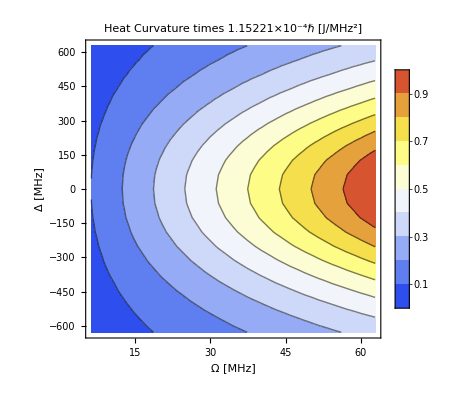

C:\Users\SurFace\Desktop\Quantum engine\3lvl_Rb.pdf

```mathematica
(* Define the Hamiltonian *)
HR[Δ_,Ω_]:=Module[{Ω1,Ω2,Δ1,Δ2},
Δ1=Δ/10; Δ2=Δ;Ω1=Ω;Ω2=Ω;
H=({{0, 0, Ω1/2}, {0, Δ1, Ω2/2}, {Ω1/2, Ω2/2, Δ2}});H];

(* Define the dissipator *)
LDiss1[r_][γd_]:=LindbladDissipator[γd*({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}),r];
LDiss2[r_][γd_]:=LindbladDissipator[γd*({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}}),r];
LD1[r_][γϕ_]:=LindbladDissipator[γϕ*({{0, 0, 0}, {0, 1, 0}, {0, 0, -1}}),r];
LD2[r_][γϕ_]:=LindbladDissipator[γϕ*({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}}),r];
diss[r_][Δ_,Ω_]:=Module[{γd=2 *π* 6.1,γϕ=0.0},
LDiss1[r][γd]+LDiss2[r][γd]+LD1[r][γϕ]+LD2[r][γϕ]];

H1=Function[{Δ,Ω},HR[Δ,Ω]];
{data,maxVal} =HeatCurvature[H1,H1,diss,{Δ,Ω},{{Δ,-2π 100,2π 100},{Ω,2π,2π 10}},{},20];

plot=ListContourPlot[
data,
ColorFunction->ColorData["TemperatureMap"],
PlotLegends->Automatic,
FrameLabel->{"Ω [MHz]","Δ [MHz]"},PlotLabel->Row[{"Heat Curvature times ",ScientificForm[maxVal],"ℏ [J/MHz^2]"}]
]

Export[FileNameJoin[{NotebookDirectory[],"3lvl_Rb.pdf"}],plot]
```

Computing Liouvillian Gap for 3x3 system...

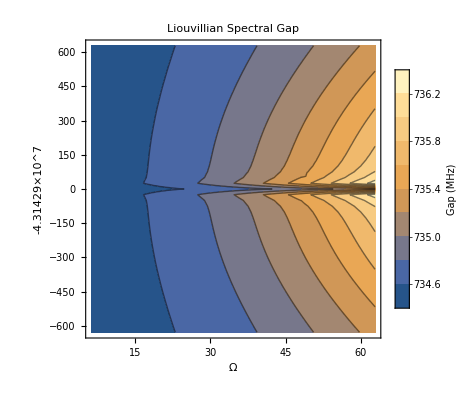

```mathematica
LiouvillianGap[H1,diss,{Δ,Ω},{{Δ,-2π 100,2π 100},{Ω,2π,2π 10}},50]
```

```mathematica
{qGeo,qDiss}=ComputeCycleHeats[
H1,
H1,(* Href=Htot *)
diss,
{Δ,Ω},{},
{-2π 100,2π},(*pMin*)
{2π 100,2π 10},(*pMax*)
100.0,(*Period tau in units of μs/2π *)
100 (*Integration points*)];
(qGeo-qDiss)*6.626*10^-34/(1.38*10^-23) (* heat change in Kelvin *)
```

Starting rectangular cycle integration for d=3 system...

--- Results ---

Geometric Heat: 3.22855

Dissipated Heat: 1.16029×10^-7

Net: 3.22855

1.55017×10^-10

## Example: Motional Hamiltonian

Mapping Heat Curvature for {Ω,F}...

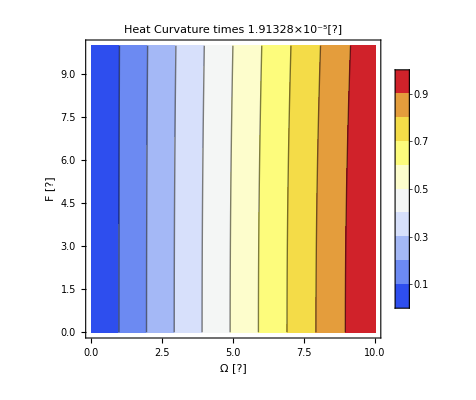

C:\Users\SurFace\Desktop\Quantum engine\motional.pdf

```mathematica
(*Define operators*)
Nmot=2;
idM=IdentityMatrix[Nmot];
idS=IdentityMatrix[2];
a=DiagonalMatrix[Sqrt[Range[Nmot-1]],1];
adag=ConjugateTranspose[a];

(*Htot Wrapper*)
Htot[Ω_,U_,F_]:=Ω*(adag.a)+(U/2)*(adag.adag.a.a)+F*(adag+a);

HtotFunc = Function[{Ω,F},Htot[Ω,1.0,F]];

LCool[r_][γc_,n_]:=γc*(n+1)*LindbladDissipator[a,r];
LHeat[r_][γh_,n_]:=γh*n*LindbladDissipator[adag,r];
L3Body[r_][γ3_]:=γ3*LindbladDissipator[a.a.a,r];

diss[r_][Ω_,F_]:=Module[{γc=1.0,γh=1.0,γ3=1.0,n=100},
LCool[r][γc,n]+LHeat[r][γh,n]+L3Body[r][γ3]];

{data,maxVal} =HeatCurvature[HtotFunc,HtotFunc,diss,{Ω,F},{{Ω,0,10},{F,0,10}},{},10];

plot=ListContourPlot[
data,
ColorFunction->ColorData["TemperatureMap"],
PlotLegends->Automatic,
FrameLabel->{"Ω [?]","F [?]"},PlotLabel->Row[{"Heat Curvature times ",ScientificForm[maxVal],"[?]"}]
]

Export[FileNameJoin[{NotebookDirectory[],"motional.pdf"}],plot]
```

## Example: Motion-TLS coupled system

Mapping Heat Curvature for {ωRF,Ω}...

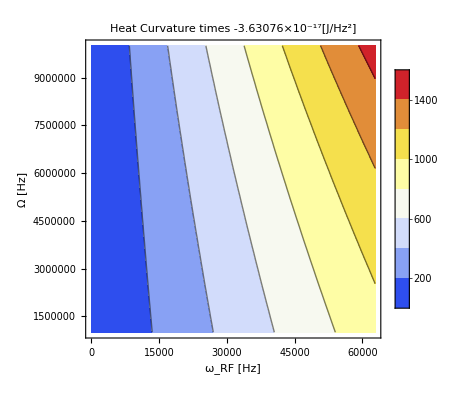

C:\Users\SurFace\Desktop\Quantum engine\motion_TLS.pdf

```mathematica
(*Define operators*)
Nmot=3;
idM=IdentityMatrix[Nmot];
idS=IdentityMatrix[2];
a=DiagonalMatrix[Sqrt[Range[Nmot-1]],1];
adag=ConjugateTranspose[a];
ℏ=1.05*10^-34;

(* 
x0 ∈ [0,10]μm, ω ∈ 2π [50,500] Hz, ωRF ∈ [1,10] MHz, Ω ∈ 2π[10,10^4]Hz
 *)

(*Htot Wrapper*)
Htot[x0_,ω_,ωRF_,Ω_]:=Module[
{μB=9.27*10^-24,B0=10^-3,dB=1.0,m=1.44*10^-25,gF=1/2},
xho= √(ℏ/(2m*ω));
η=gF*μB*xho*dB/ℏ;
Δ=ωRF-(μB *gF* B0)/ℏ;
Hmot = KroneckerProduct[σ0,ω*(adag.a-x0/xho*(adag+a))];
Hspin =KroneckerProduct[ 1/2(Δ*σ3+Ω*σ1),IdentityMatrix[Nmot]];
Hcoup =KroneckerProduct[σ3,-η*(adag+a)];
Hmot+Hspin+Hcoup];

HtotFunc = Function[{ωRF,Ω},Htot[10^-5,2π 500,ωRF,Ω]];
HRefFunc[ωRF_,Ω_]:=KroneckerProduct[idS,1.0*(adag.a)];

(* Define the dissipator *)
LOP[r_][γup_]:=LindbladDissipator[√γup*KroneckerProduct[σup,IdentityMatrix[Nmot]],r];
LDP[r_][γϕ_]:=LindbladDissipator[√(γϕ/2)*KroneckerProduct[σ3,IdentityMatrix[Nmot]],r];
LC[r_][Γm_,n_]:=LindbladDissipator[√(Γm*(n+1))*KroneckerProduct[σ0,a],r];
LH[r_][Γm_,n_]:=LindbladDissipator[√(Γm*n)*KroneckerProduct[σ0,adag],r];
diss[r_][ωRF_,Ω_]:=Module[{γup=10^3,γϕ=1.0,Γm=1.0,n=100},
(LOP[r][γup]+LDP[r][γϕ]+LC[r][Γm,n]+LH[r][Γm,n])];

(*Compute the Heat Curvature Map*)
{data,maxVal} =HeatCurvature[HtotFunc,HRefFunc,diss,{ωRF,Ω},{{ωRF,10^6,10^7},{Ω,2π 10,2π 10^4}},{},20];

plot=ListContourPlot[
data,
ColorFunction->ColorData["TemperatureMap"],
PlotLegends->Automatic,
FrameLabel->{"ω_RF [Hz]","Ω [Hz]"},PlotLabel->Row[{"Heat Curvature times ",ScientificForm[maxVal],"[J/Hz^2]"}]
]

Export[FileNameJoin[{NotebookDirectory[],"motion_TLS.pdf"}],plot]
```

Computing Liouvillian Gap for 6x6 system...

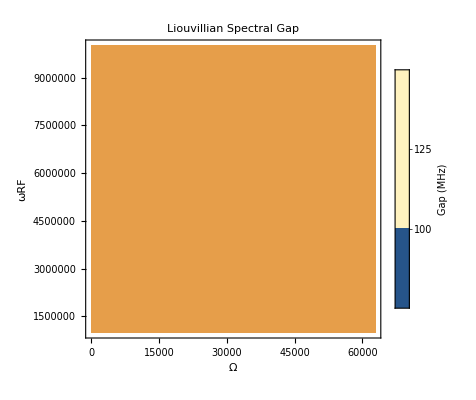

```mathematica
LiouvillianGap[HtotFunc,diss,{ωRF,Ω},{{ωRF,10^6,10^7},{Ω,2π 10,2π 10^4}},50]
```

```mathematica
{qGeo,qDiss}=ComputeCycleHeats[
HtotFunc,
HRefFunc,
diss,
{ωRF,Ω},{},
{1.0*10^6,2π 10},(*pMin*)
{1.0*10^7,2π 10^4},(*pMax *)
500.0,(*Period tau in units of μs/2π *)
50 (*Integration points*)];

(qGeo-qDiss)*ℏ/(1.38*10^-23) (* heat change in Kelvin *)
```

Starting rectangular cycle integration for d=6 system...

--- Results ---

Geometric Heat: 1.58155×10^-6

Dissipated Heat: 5.48568×10^-12

Net: 1.58156×10^-6

1.20335×10^-17

## Example (just the model): The Scovil-Schulz-DuBois (SSDB) Maser

```mathematica
H=(E1*id+(E2-E1)*gm[3]+(E3-E1)*gm[8]+Omega*(gm[6]))/.{E3->Δ,E2->Δ/2,E1->0}; 

HotDown={{0,0,1},{0,0,0},{0,0,0}}; 
HotUp=ConjugateTranspose[HotDown];     
ColdDown={{0,1,0},{0,0,0},{0,0,0}}; 
ColdUp=ConjugateTranspose[ColdDown];

Dissipators=Function[r,γh*LindbladDissipator[HotDown,r]+γh*LindbladDissipator[HotUp,r]+γc*LindbladDissipator[ColdDown,r]+γc*LindbladDissipator[ColdUp,r]];
```

## Example (just the model): The Quantum Absorption Refrigerator

```mathematica
(*Jump operators for the three reservoirs*)
ColdDown={{0,1,0},{0,0,0},{0,0,0}};
ColdUp={{0,0,0},{0,1,0},{0,0,0}};
WorkDown={{0,0,0},{0,0,1},{0,0,0}};
WorkUp={{0,0,0},{0,0,0},{0,1,0}};
HotDown={{0,0,1},{0,0,0},{0,0,0}};
HotUp={{0,0,0},{0,0,0},{1,0,0}};
nc = nBE[Δ1-Δ2,Tc]/.{Δ1->Δ,Δ2->Δ/2,Tc->1.0};
nw = nBE[Δ2,Tw]/.{Δ1->Δ,Δ2->Δ/2,Tw->2.0};
nh=nBE[Δ1,Th]/.{Δ1->Δ,Δ2->Δ/2,Th->2.0};
(*In the master equation,you'd add terms for each with rates proportional to the Bose-Einstein distribution n_B(T) and n_B(T)+1*)

H=({{0, 0, Ω1/2}, {0, Δ1-Δ2, Ω2/2}, {Ω1/2, Ω2/2, Δ1}})/.{Ω1->Ω,Ω2->Ω, Δ1->Δ,Δ2->Δ/2};

DissCold=Function[r,γc*(nc+1)*LindbladDissipator[ColdDown,r]+γc*nc*LindbladDissipator[ColdUp,r]];
DissHot=Function[r,γh*(nh+1)*LindbladDissipator[HotDown,r]+γh*nh*LindbladDissipator[HotUp,r]];
DissWork=Function[r,γw*(nw+1)*LindbladDissipator[WorkDown,r]+γw*nw*LindbladDissipator[WorkUp,r]];

Dissipators =Function[r,( DissCold[r] + DissHot[r ]+ DissWork[r])/.{γc->γ,γh->γ,γw->γ}];
```